### From https://www.thphys.uni-heidelberg.de/~plehn/includes/notes/hunting_higgs/hunting_higgs.pdf (Eq.48) (note that in Eq.48 there is one sign wrong) τ=4 mQ^2/m_H^2

```mathematica
$Assumptions=τ>0 && x>0 && τ ∈Reals
```

τ>0&&x>0&&τ∈ℝ

```mathematica
f[τ_]:=If[τ>1,(ArcSin[1/(√τ)]^2),-1/4(Log[(1+√(1-τ))/(1-√(1-τ))]-I Pi)^2];
F[τ_]:=3/2 τ(1+(1-τ)f[τ]);
(* Define a function corresponding to |F[τ]|^2 for avoiding dealing with imaginary couplings *)
fheavy2[τ_]=(Re[(Expand[Simplify[F[τ],Assumptions->τ<1]])]/.{Im[a_]->0,Re[a_]->a})^2 +(Im[(Expand[Simplify[F[τ],Assumptions->τ<1]])]/.{Im[a_]->0,Re[a_]->a})^2 ;
sert[x_]=Simplify[Normal[Series[Simplify[F[τ],Assumptions->τ>1]/.{τ->1/x},{x,0,3}]]];
fLight[x_]:=Simplify[F[τ],Assumptions->τ>1]/.{τ->1/x};
fHeavy[x_]=Simplify[
Normal[Series[Simplify[F[τ],Assumptions->τ<1],{τ,0,3}]]/.{τ->1/x}];
```

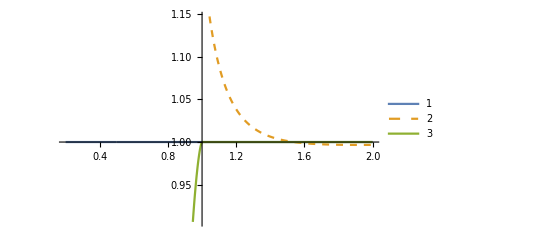

```mathematica
Plot[{Abs[fLight[x]]^2/Abs[F[1/x]]^2,Abs[fHeavy[x]]^2/Abs[F[1/x]]^2,fheavy2[1/x]/Abs[F[1/x]]^2},{x,0.2,2},PlotLegends->Automatic,PlotStyle->{Thick,Dashed},AxesOrigin->{1.,1.}]
```

Expression in FeynRules:

```mathematica
InputForm[Simplify[fheavy2[1/x],Assumptions->{x>1}]]
```

(9*((Pi^2*(-1 + x) + 4*x)^2 + 2*(Pi^2*(-1 + x) - 4*x)*(-1 + x)*Log[(1 + Sqrt[(-1 + x)/x])/(1 - Sqrt[(-1 + x)/x])]^2 + (-1 + x)^2*Log[(1 + Sqrt[(-1 + x)/x])/(1 - Sqrt[(-1 + x)/x])]^4))/(64*x^4)

Cubic expansion for light Higgs:

```mathematica
sert[x]
```

1+(7 x)/30+(2 x^2)/21+(26 x^3)/525